```mathematica
(*C*)
```

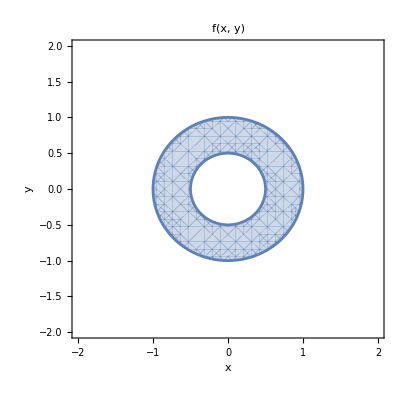

```mathematica
f[x_,y_]:=If[1/2<=Sqrt[x^2+y^2]<=1,1,0]
RegionPlot[f[x,y]==1,{x,-2,2},{y,-2,2},FrameLabel->{"x","y"},PlotLegends->Automatic,PlotLabel->"f(x, y)"]
```

```mathematica
(*D*)
(*pierścień*)
```

```mathematica
calka= Integrate[f[x,y],{x,-1,1},{y,-1,1}]
```

(3 π)/4

```mathematica
(*małe koło*)
```

```mathematica
Simplify[π-calka]
```

π/4